Mathe starting

Prestazioni Mathe: 
 Media per singolo frame: 0.12218
 Tempo massimo per singolo frame: 0.16743
 Tempo minimo per singolo frame: 0.10939
 Tempo totale per 10 frame: 1.22329

Simple starting

Prestazioni simple: 
 Media per singolo frame: 0.412765
 Tempo massimo per singolo frame: 0.693223
 Tempo minimo per singolo frame: 0.373834
 Tempo totale per 10 frame: 4.129101

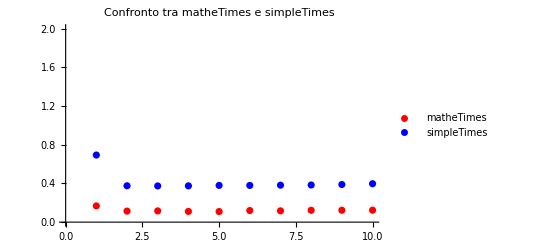

```mathematica
(*---Precompilazione delle funzioni numeriche---*)(*Funzione compilata per la binarizzazione:prende in ingresso una matrice (data) e una soglia (thresh) e restituisce una matrice binaria*)compiledBinarize=Compile[{{data,_Real,2},{thresh,_Real}},
Map[If[#>thresh,1,0]&,data,{2}],
CompilationTarget->"C",RuntimeOptions->"Speed"];

(*Funzione compilata per la dilatazione:prende in ingresso una matrice binaria (data) e una matrice strutturante (se) ed esegue la dilatazione (ricorda:per dilatazione,se un qualsiasi pixel della "finestra" moltiplicato per se dà 1,allora il risultato è 1)*)
compiledDilationSimple=Compile[{{data,_Real,2},{se,_Real,2}},Module[{conv},conv=ListConvolve[se,data,{1,1},0];
Map[If[#>=1,1,0]&,conv,{2}]],CompilationTarget->"C",RuntimeOptions->"Speed"];


(*---Funzioni personalizzate che sfruttano le versioni compilate---*)

(*Binarizzazione "semplice" usando la funzione compilata*)
simpleBinarize[img_Image]:=Module[{gray,data,thresh,binaryData},
gray=ColorConvert[img,"Grayscale"];
(*conversione in scala di grigi*)
data=ImageData[gray];
(*estrazione della matrice dei pixel*)
thresh=Mean[Flatten[data]];
(*soglia basata sulla media dei valori*)
binaryData=compiledBinarize[data,thresh];
Image[binaryData,"Bit"]];

simpleDilation[img_Image,se_?MatrixQ]:=Module[{data,result},data=ImageData[img];
result=compiledDilationSimple[data,N[se]];
Image[result,"Bit"]];


(*FillingTransform semplice non è stata precompilata,poiché richiede operazioni non strettamente numeriche*)
simpleFillingTransform[img_Image]:=Module[{data,dims,compImg,binImg,comp,borderIDs,holeMask,filledData},data=ImageData[img];
dims=Dimensions[data];
compImg=1-data;(*complementare*)binImg=Binarize[Image[compImg]];
comp=MorphologicalComponents[binImg];
borderIDs=DeleteDuplicates[Flatten[{comp[[1,All]],(*bordo superiore*)comp[[dims[[1]],All]],(*bordo inferiore*)comp[[All,1]],(*bordo sinistro*)comp[[All,dims[[2]]]]    (*bordo destro*)}]];
holeMask=Map[If[#!=0&&Not[MemberQ[borderIDs,#]],1,0]&,comp,{2}];
filledData=MapThread[Max[#1,#2]&,{data,holeMask},2];
Image[filledData,"Bit"]];

(*---Funzioni principali---*)

(*Funzione che usa le funzioni built-in di Mathematica*)
matheFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},SetDirectory[NotebookDirectory[]];
img=Import[foto];
img=ImageResize[img,Scaled[0.5]];
imgBin=Binarize[img];
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=Dilation[edges,DiskMatrix[1]];
filledImage=FillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}];
misure];

(*Funzione che usa le versioni "semplici" precompilate per la binarizzazione e la dilatazione*)
simpleFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},SetDirectory[NotebookDirectory[]];
img=Import[foto];
img=ImageResize[img,Scaled[0.5]];
imgBin=simpleBinarize[img];(*uso della versione compilata per la binarizzazione*)imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=simpleDilation[edges,DiskMatrix[1]];(*uso della versione compilata per la dilatazione*)filledImage=simpleFillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}];
misure];

(*---Valutazione delle prestazioni---*)

SetDirectory[NotebookDirectory[]];
foto="foto5.jpg";

matheTimes={};
simpleTimes={};

Print["Mathe starting"];
tot=AbsoluteTime[];
For[i=0,i<10,i++,time=AbsoluteTime[];
matheFunc[foto];
timer=AbsoluteTime[]-time;
AppendTo[matheTimes,timer];];
totm=AbsoluteTime[]-tot;
Print["Prestazioni Mathe: \n Media per singolo frame: ",Mean[matheTimes],"\n Tempo massimo per singolo frame: ",Max[matheTimes],"\n Tempo minimo per singolo frame: ",Min[matheTimes],"\n Tempo totale per 10 frame: ",totm];

Print["Simple starting"];
tot=AbsoluteTime[];
For[i=0,i<10,i++,times=AbsoluteTime[];
simpleFunc[foto];
timers=AbsoluteTime[]-times;
AppendTo[simpleTimes,timers];];
tots=AbsoluteTime[]-tot;
Print["Prestazioni simple: \n Media per singolo frame: ",Mean[simpleTimes],"\n Tempo massimo per singolo frame: ",Max[simpleTimes],"\n Tempo minimo per singolo frame: ",Min[simpleTimes],"\n Tempo totale per 10 frame: ",tots];

ListPlot[{matheTimes,simpleTimes},PlotLegends->{"matheTimes","simpleTimes"},PlotStyle->{Red,Blue},PlotLabel->"Confronto tra matheTimes e simpleTimes",PlotRange->{{Automatic,Automatic},{0,2}}]
```